```mathematica
f[n_] := 2^n
```

```mathematica
g[n_] := 2^n/(Sqrt[2*Pi*n])
```

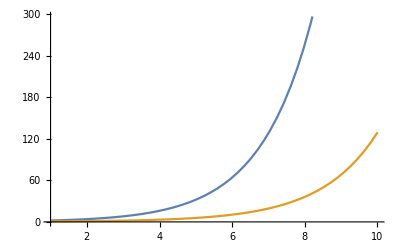

```mathematica
Plot[{f[n],g[n]},{n,1,10}]
```

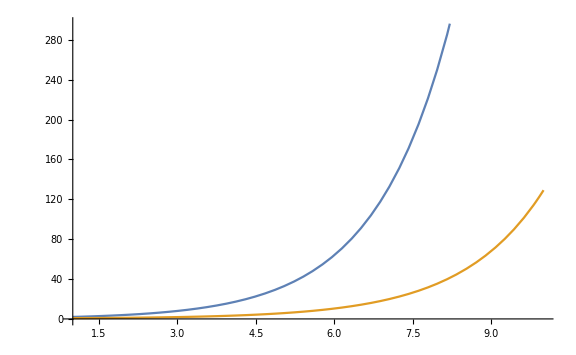

```mathematica
Show[%15,ImageSize->Large]
```

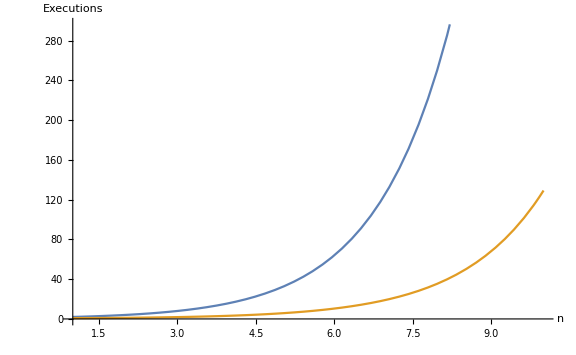

```mathematica
Show[%22,AxesLabel->{HoldForm[n],HoldForm[Executions]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/Users/jp/Documents/minhit-fig.pdf",%23,"PDF"]
```

/Users/jp/Documents/minhit-fig.pdf